```mathematica
ClearAll["Global`*"];
```

```mathematica
ising=Table[2RandomInteger[]-1,{i,1,50,1},{j,1,50,1}];
MatrixForm[ising];
```

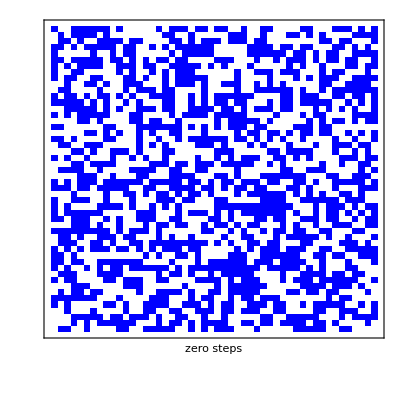

```mathematica
ArrayPlot[ising,ColorRules->{1->Blue,-1->White},Frame->True,FrameLabel->{""  ,"zero  steps"} ]
```

(a) define a function “flip” to flip spins.

```mathematica
flip=-ising[[RandomInteger[{1,50}],RandomInteger[{1,50}]]]
```

1

(b) ising magnet after 1000 steps

```mathematica
J=0.5;
m={1/2500 Sum[ising[[i]][[j]],{i,1,50},{j,1,50}]};
```

```mathematica
ising=Table[2RandomInteger[]-1,{i,1,50,1},{j,1,50,1}];
```

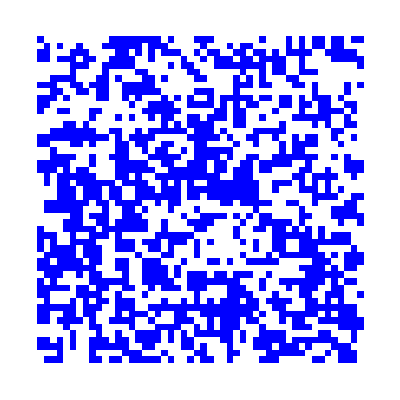

```mathematica
Do[{i1,i2}={RandomInteger[{1,50}],RandomInteger[{1,50}]};
If[i1==50,dn=1,dn=i1+1];
If[i2==50,rt=1,rt=i2+1];
If[i1==1,up=50,up=i1-1];
If[i2==1,lt=50,lt=i2-1];
neighborspin=ising[[dn,i2]]+ising[[up,i2]]+ising[[i1,rt]]+ising[[i1,lt]];

δE=2ising[[i1,i2]] J neighborspin;If[δE<0,ising[[i1,i2]]=-ising[[i1,i2]],If[Random[]<Exp[-δE],ising[[i1,i2]]=-ising[[i1,i2]],ising[[i1,i2]]=ising[[i1,i2]]]];mm=1/2500 Sum[ising[[i]][[j]],{i,1,50},{j,1,50}];m=Append[m,mm],{1000}];
ArrayPlot[ising,ColorRules->{1->Blue,-1->White},FrameLabel->{" " ,"1000 steps"}]
```

(c) ising magnet after 5000 steps

```mathematica
ising=Table[2RandomInteger[]-1,{i,1,50,1},{j,1,50,1}];
```

```mathematica
m={1/2500 Sum[ising[[i]][[j]],{i,1,50},{j,1,50}]};
```

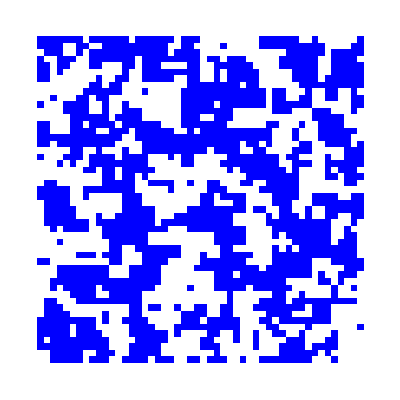

```mathematica
Do[{i1,i2}={RandomInteger[{1,50}],RandomInteger[{1,50}]};
If[i1==50,dn=1,dn=i1+1];
If[i2==50,rt=1,rt=i2+1];
If[i1==1,up=50,up=i1-1];
If[i2==1,lt=50,lt=i2-1];
neighborspin=ising[[dn,i2]]+ising[[up,i2]]+ising[[i1,rt]]+ising[[i1,lt]];

δE=2ising[[i1,i2]] J neighborspin;If[δE<0,ising[[i1,i2]]=-ising[[i1,i2]],If[Random[]<Exp[-δE],ising[[i1,i2]]=-ising[[i1,i2]],ising[[i1,i2]]=ising[[i1,i2]]]];mm=1/2500 Sum[ising[[i]][[j]],{i,1,50},{j,1,50}];m=Append[m,mm],{5000}];
ArrayPlot[ising,ColorRules->{1->Blue,-1->White},FrameLabel->{" " ,"5000 steps"}]
```

(d) ising magnet after 10000 steps

```mathematica
ising=Table[2RandomInteger[]-1,{i,1,50,1},{j,1,50,1}];
```

```mathematica
m={1/2500 Sum[ising[[i]][[j]],{i,1,50},{j,1,50}]};
```

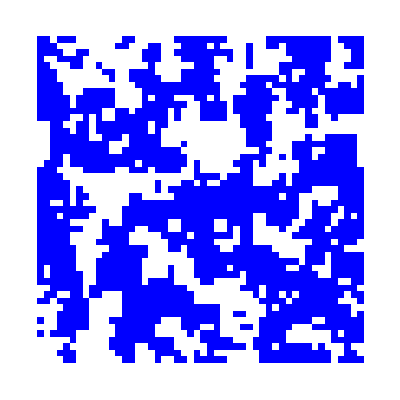

```mathematica
Do[{i1,i2}={RandomInteger[{1,50}],RandomInteger[{1,50}]};
If[i1==50,dn=1,dn=i1+1];
If[i2==50,rt=1,rt=i2+1];
If[i1==1,up=50,up=i1-1];
If[i2==1,lt=50,lt=i2-1];
neighborspin=ising[[dn,i2]]+ising[[up,i2]]+ising[[i1,rt]]+ising[[i1,lt]];

δE=2ising[[i1,i2]] J neighborspin;If[δE<0,ising[[i1,i2]]=-ising[[i1,i2]],If[Random[]<Exp[-δE],ising[[i1,i2]]=-ising[[i1,i2]],ising[[i1,i2]]=ising[[i1,i2]]]];m=Append[m,Abs[Apply[Plus,Flatten[ising]]/2500]],{i,1,10000}];
ArrayPlot[ising,ColorRules->{1->Blue,-1->White},FrameLabel->{" " ,"10000 steps"}]
```

(e) plot the trajectory after 10000 steps

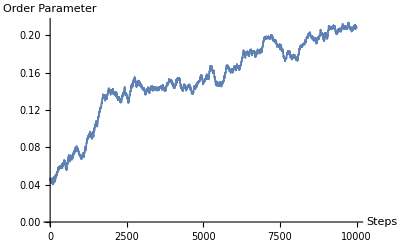

```mathematica
ListPlot[m,AxesLabel->{"Steps","Order Parameter"}]
```